### Start choosing the example:

```mathematica
t=31;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5},Adjacency Matrix→{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{5,U1}},Switching Costs→{}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 80, U1-> 15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.020779,Null}

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j13→80.,j14→80.,j15→80.,j16→80.,j17→80.,j18→80.,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80.,jt27→80.,jt28→0.,jt29→80.,jt30→0.,jt31→80.,jt32→0.,jt33→80.,jt34→0.,u35→335.,u36→255.,u37→175.,u38→95.,u39→15.,u40→335.,u41→255.,u42→175.,u43→95.,u44→15.,u45→15.,u46→335.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.2945×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.2945×10^-17

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→25.3278,u36→22.7459,u37→20.1639,u38→17.582,u39→15.,u40→25.3278,u41→22.7459,u42→20.1639,u43→17.582,u44→15.,u45→15.,u46→25.3278|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.2472×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.2472×10^-17

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→27.6454,u36→24.484,u37→21.3227,u38→18.1613,u39→15.,u40→27.6454,u41→24.484,u42→21.3227,u43→18.1613,u44→15.,u45→15.,u46→27.6454|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.42154×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.42154×10^-16

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→35.0956,u36→30.0717,u37→25.0478,u38→20.0239,u39→15.,u40→35.0956,u41→30.0717,u42→25.0478,u43→20.0239,u44→15.,u45→15.,u46→35.0956|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→194.864,u36→149.898,u37→104.932,u38→59.966,u39→15.,u40→194.864,u41→149.898,u42→104.932,u43→59.966,u44→15.,u45→15.,u46→194.864|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.7053×10^-13

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→335.,u36→255.,u37→175.,u38→95.,u39→15.,u40→335.,u41→255.,u42→175.,u43→95.,u44→15.,u45→15.,u46→335.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.00439×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.00439×10^-16

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→1470.62,u36→1106.72,u37→742.811,u38→378.906,u39→15.,u40→1470.62,u41→1106.72,u42→742.811,u43→378.906,u44→15.,u45→15.,u46→1470.62|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→91376.9,u36→68536.4,u37→45695.9,u38→22855.5,u39→15.,u40→91376.9,u41→68536.4,u42→45695.9,u43→22855.5,u44→15.,u45→15.,u46→91376.9|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→1.16019×10^6,u36→870144.,u37→580101.,u38→290058.,u39→15.,u40→1.16019×10^6,u41→870144.,u42→580101.,u43→290058.,u44→15.,u45→15.,u46→1.16019×10^6|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→1.16379×10^6,u36→872843.,u37→581900.,u38→290958.,u39→15.,u40→1.16379×10^6,u41→872843.,u42→581900.,u43→290958.,u44→15.,u45→15.,u46→1.16379×10^6|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→1.35676×10^6,u36→1.01758×10^6,u37→678389.,u38→339202.,u39→15.,u40→1.35676×10^6,u41→1.01758×10^6,u42→678389.,u43→339202.,u44→15.,u45→15.,u46→1.35676×10^6|>

```mathematica
alpha = 1.61;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.85029×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.85029×10^-16

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→1.59226×10^6,u36→1.1942×10^6,u37→796137.,u38→398076.,u39→15.,u40→1.59226×10^6,u41→1.1942×10^6,u42→796137.,u43→398076.,u44→15.,u45→15.,u46→1.59226×10^6|>

```mathematica
alpha = 1.62;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.20055×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.20055×10^-16

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→2.21748×10^6,u36→1.66311×10^6,u37→1.10875×10^6,u38→554381.,u39→15.,u40→2.21748×10^6,u41→1.66311×10^6,u42→1.10875×10^6,u43→554381.,u44→15.,u45→15.,u46→2.21748×10^6|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→6.61557×10^6,u36→4.96168×10^6,u37→3.30779×10^6,u38→1.6539×10^6,u39→15.,u40→6.61557×10^6,u41→4.96168×10^6,u42→3.30779×10^6,u43→1.6539×10^6,u44→15.,u45→15.,u46→6.61557×10^6|>

```mathematica
alpha = 1.7;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.77757×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.77757×10^-16

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→6.238×10^7,u36→4.6785×10^7,u37→3.119×10^7,u38→1.5595×10^7,u39→15.,u40→6.238×10^7,u41→4.6785×10^7,u42→3.119×10^7,u43→1.5595×10^7,u44→15.,u45→15.,u46→6.238×10^7|>

```mathematica
alpha = 1.8;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.34393×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.34393×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.34393×10^-16

«7 more identical outputs»

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→9.62104×10^10,u36→7.21578×10^10,u37→4.81052×10^10,u38→2.40526×10^10,u39→15.,u40→9.62104×10^10,u41→7.21578×10^10,u42→4.81052×10^10,u43→2.40526×10^10,u44→15.,u45→15.,u46→9.62104×10^10|>

```mathematica
alpha = 1.89;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.85361×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.85361×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.85361×10^-16

«7 more identical outputs»

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→8.35229×10^17,u36→6.26422×10^17,u37→4.17614×10^17,u38→2.08807×10^17,u39→15.,u40→8.35229×10^17,u41→6.26422×10^17,u42→4.17614×10^17,u43→2.08807×10^17,u44→15.,u45→15.,u46→8.35229×10^17|>

```mathematica
alpha = 1.9;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.65473×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.65473×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.65473×10^-16

«7 more identical outputs»

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→2.24148×10^19,u36→1.68111×10^19,u37→1.12074×10^19,u38→5.6037×10^18,u39→15.,u40→2.24148×10^19,u41→1.68111×10^19,u42→1.12074×10^19,u43→5.6037×10^18,u44→15.,u45→15.,u46→2.24148×10^19|>

```mathematica
alpha = 1.95;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→3.01738×10^33,u36→2.26303×10^33,u37→1.50869×10^33,u38→7.54344×10^32,u39→15.,u40→3.01738×10^33,u41→2.26303×10^33,u42→1.50869×10^33,u43→7.54344×10^32,u44→15.,u45→15.,u46→3.01738×10^33|>

```mathematica
alpha = 1.99;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.11662×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.11662×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.11662×10^-16

«7 more identical outputs»

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→7.96243×10^105,u36→5.97182×10^105,u37→3.98121×10^105,u38→1.99061×10^105,u39→15.,u40→7.96243×10^105,u41→5.97182×10^105,u42→3.98121×10^105,u43→1.99061×10^105,u44→15.,u45→15.,u46→7.96243×10^105|>

```mathematica
alpha = 1.999;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.35007×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.35007×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.35007×10^-16

«7 more identical outputs»

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→6.93439×10^106,u36→5.20079×10^106,u37→3.46719×10^106,u38→1.7336×10^106,u39→15.,u40→6.93439×10^106,u41→5.20079×10^106,u42→3.46719×10^106,u43→1.7336×10^106,u44→15.,u45→15.,u46→6.93439×10^106|>

```mathematica
alpha = 2;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.69547×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.69547×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.69547×10^-16

«17 more identical outputs»

<|j13→80,j14→80,j15→80,j16→80,j17→80,j18→80,j19→0.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,jt25→0.,jt26→80,jt27→80,jt28→0.,jt29→80,jt30→0.,jt31→80,jt32→0.,jt33→80,jt34→0.,u35→8.81959×10^106,u36→6.61469×10^106,u37→4.4098×10^106,u38→2.2049×10^106,u39→15.,u40→8.81959×10^106,u41→6.61469×10^106,u42→4.4098×10^106,u43→2.2049×10^106,u44→15.,u45→15.,u46→8.81959×10^106|>

### What we this plot for?

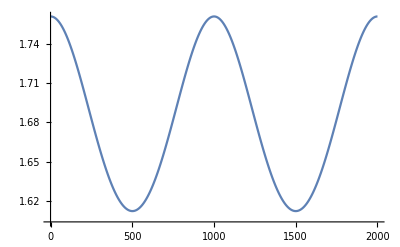

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.